```mathematica
Exit[];
```

```mathematica
eq2:={x1''[t]==-x1[t]+0.5  x2[t],x2''[t]==0.5  x1[t]-  x2[t],x1[0]==1,x1'[0]==x2[0]==x2'[0]==0}
```

```mathematica
NDSolve[eq2, {x1[t], x2[t]}, {t, 0, 2}]
```

{{x1[t]→InterpolatingFunction[…][t],x2[t]→InterpolatingFunction[…][t]}}

```mathematica
{x1ans[t_], x2ans[t_]} = {x1[t], x2[t]} /. Flatten[NDSolve[eq2, {x1[t], x2[t]}, {t, 0, 2}]]
```

{InterpolatingFunction[…][t],InterpolatingFunction[…][t]}

```mathematica
graphx1 = Plot[x1ans[t], {t, 0, 2}, AxesLabel -> {"t", "y"}, PlotLabel -> "Numerical Solution of Equation 1"];
```

```mathematica
graphx2 = Plot[x2ans[t], {t, 0, 2}, AxesLabel -> {"t", "y"}, PlotLabel -> "Numerical Solution of Equation 2"];
```

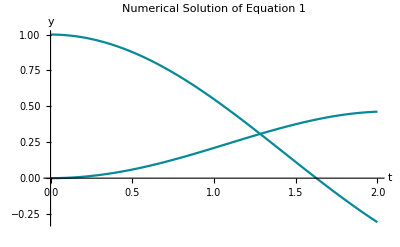

```mathematica
Show[graphx1, graphx2]
```